# Lecture 5 - Collisions

### A Puzzle...

Let us compute the Lorentz transformation of a Lorentz transformation. Suppose a frame S' moves at velocity v_1 to the right with respect to a frame S, and furthermore that there is another frame S'' which sees S as moving to the right with a velocity v_2. What is the Lorentz transformation between frames S' and S''?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
Let us define the two γ’s in this problem as

γ_1=1/((1-{v_1/c}^2)^(1/2))
γ_2=1/((1-{v_2/c}^2)^(1/2))

The Lorentz transformation between S and S' is given by

Δ,x'=γ_1 (Δ,x-v_1 Δ,t)
Δ,t'=γ_1 (Δ,t-v_1/c^2 Δ,x)

Similarly, the Lorentz transformation between S'' and S is given by

Δ,x=γ_2 (Δ,x''-v_2 Δ,t'')
Δ,t=γ_2 (Δ,t''-v_2/c^2 Δ,x'')

Substituting in these latter two relations into the former two relations,

Δ,x'=γ_1 (γ_2 (Δ,x''-v_2 Δ,t'')-v_1 γ_2 (Δ,t''-v_2/c^2 Δ,x''))
=γ_1 γ_2 ((1+(v_1 v_2)/c^2)Δ,x''-(v_1+v_2) Δ,t'')

Δ,t'=γ_1 (γ_2 (Δ,t''-v_2/c^2 Δ,x'')-v_1/c^2 γ_2 (Δ,x''-v_2 Δ,t''))
=γ_1 γ_2 (-(v_1+v_2)/c^2Δ,x''+(1+(v_1 v_2)/c^2) Δ,t'')

At this point, we will take an inspired guess, and define a velocity

v=(v_1+v_2)/(1+(v_1 v_2)/c^2)

and its associated γ factor

γ=1/({1-(v/c)^2}^(1/2))
=1/({1-(((v_1+v_2)/c)/(1+(v_1 v_2)/c^2))^2}^(1/2))                (multiply numerator and denominator by (1+(v_1 v_2)/c^2))
=(1+(v_1 v_2)/c^2)/({(1+(v_1 v_2)/c^2)^2-((v_1+v_2)/c)^2}^(1/2))
=(1+(v_1 v_2)/c^2)/({(1+(2 v_1 v_2)/c^2+(v_1^2 v_2^2)/c^4)-((v_1^2+2 v_1 v_2+v_2^2)/c^2)}^(1/2))
=(1+(v_1 v_2)/c^2)/({1-v_1^2/c^2-v_2^2/c^2+(v_1^2 v_2^2)/c^4}^(1/2))
=(1+(v_1 v_2)/c^2)/({(1-{v_1/c}^2)(1-{v_2/c}^2)}^(1/2))
=γ_1 γ_2(1+(v_1 v_2)/c^2)

Using Equations (TextNumbered) and (TextNumbered), we can greatly simplify the double Lorentz transformation Equations (TextNumbered) and (TextNumbered) into

Δ,x'=γ_1 γ_2 ((1+(v_1 v_2)/c^2)Δ,x''-(v_1+v_2) Δ,t'')
=γ (Δ,x''-(v_1+v_2)/(1+(v_1 v_2)/c^2) Δ,t'')
=γ (Δ,x''-v Δ,t'')

Δ,t'=γ_1 γ_2 (-(v_1+v_2)/c^2Δ,x''+(1+(v_1 v_2)/c^2) Δ,t'')
=γ (-1/c^2(v_1+v_2)/(1+(v_1 v_2)/c^2)Δ,x''+Δ,t'')
=γ (Δ,t''-v/c^2 Δ,x'')

The algebra above was a mess, but look at how clean the results are! You will recognize these final two relations as a Lorentz transformation between frame S' and S'', assuming that S' moves to the right with velocity v=(v_1+v_2)/(1+(v_1 v_2)/c^2).

Indeed, we could have predicted all of these results in hindsight. First of all, the Lorentz transformation of a Lorentz transformation must be another Lorentz transformation so that our theory is consistent. To be precise, any two inertial reference frames must be related by a Lorentz transformation. If this was false, then the second postulate of Special Relativity (that all inertial frames are “equivalent”) would have to be thrown out.

Furthermore, Equation (TextNumbered) is nothing more than velocity addition, as we would expect since from the S'' frame’s perspective, frame S' is travelling at a speed found by relativistically combining the velocities v_1 and v_2. So everything is consistent in our theory! □

### Energy and Momentum

#### The Results

The momentum and energy of a particle equal

p⃗=γ m v⃗

E=γ m c^2

where γ=1/((1-v^2/c^2)^(1/2)). Notice that when v≪c, these expressions expand to

p⃗≈m v⃗+O[(v/c)^3]

E≈m c^2 (1+v^2/(2 c^2)+···)≈m c^2+1/2 m v^2+O[(v/c)^4]

The former is simply the definition of momentum that we know and love from Newtonian mechanics. The latter is the energy of a particle, 1/2 m v^2 (we are assuming no potentials, and therefore no potential energy) plus the m c^2, which is Einstein’s famous formula for the rest energy of a mass m.

#### An Important Relation

Note the following important relation

E^2-(|p⃗|)^2 c^2=γ^2 m^2 c^4-γ^2 m^2(|v⃗|)^2 c^2
=γ^2 m^2 c^4 (1-v^2/c^2)
=m^2 c^4

This equation will be our primary ingredient in solving relativistic collision problems. We can write it equivalently as

E^2=p^2 c^2+m^2 c^4

In the case where m=0 (as for photons), we obtain E=p c. This is a key equation for massless objects, since p⃗=γ m v⃗ and E=γ m c^2 don’t tell us much when m=0 and thus γ=∞ (since massless particles must travel at speed c to have a non-zero energy (any particle that only has zero energy wouldn’t interact with the world in any way)).

Another nice relation is found by diving p⃗=γ m v⃗ by E=γ m c^2 to obtain

(p⃗)/E=(v⃗)/c^2

#### Complementary Section: The Size of m c^2

Consider a mass m=1kg. Then m c^2=(1kg)(3 10^8 m/s)^2≈10^17 J. How big is this? A typical household electric bill might be $50 per month, or $600 per year. At about 10 centers per kilowatt-hour, this translates to 6000 kilowatt-hours per year. Since there are 3600 seconds in an hour, this converts to (6000)(10^3)(3600)≈2 10^10 watt-seconds. That is, 2 10^10 joules per year. We therefore see that if one kilogram were converted completely into usable energy, it would be enough to provide electricity to 10^17/(2 10^10), or 5 million, homes for a year. That’s a lot!

In a nuclear reactor, only a small fraction of the mass energy is converted into usable energy. Most of the mass remains in the final products, which doesn't help in lighting up your home. If a particle were to combine with its antiparticle, then it would be possible for all of the mass energy to be converted into usable energy. But we're still a few years away from this.

However, even a small fraction of the very large quantity, E=m c^2, can still be large, as evidenced by the use of nuclear power and nuclear weapons. Any quantity with a few factors of c is bound to change the face of the world.

#### Transforming E and p⃗

Consider the following one-dimensional situation, where all the motion is along the x-axis. A particle has energy E' and momentum p' in frame S' . Frame S' moves at speed v with respect to frame S, in the positive x-direction. What are E and p in S?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Let u' be the particle’s speed in S' . From the velocity addition formula, the particle’s speed in S is

u/c=(u'/c+v/c)/(1+u'v/c^2)

This is all we need to know, because a particle’s velocity determines its energy and momentum. But we’ll need to go through a little algebra to make things look pretty. The γ factor associated with the speed u is

γ_u=1/((1-((u'/c+v/c)/(1+u'v/c^2))^2)^(1/2))=(1+u'v/c^2)/(((1+u'v/c^2)^2-(u'/c+v/c)^2)^(1/2))
=(1+u'v/c^2)/((1-(u'/c)^2-(v/c)^2+(u'v/c^2)^2)^(1/2))=(1+u'v/c^2)/({1-u'/c}{1-v/c})^(1/2)
=γ_u' γ_v (1+u'v/c^2)

The energy and momentum in S' are

E'=γ_u' m c^2

p'=γ_u' m u'

while the energy and momentum in S are

E=γ_u m c^2=γ_u' γ_v (1+u'v/c^2)m c^2

p=γ_u m u=γ_u' γ_v (1+u'v/c^2)m (u'+v)/(1+u'v/c^2)=γ_u' γ_v m (u'+v)

We can now rewrite E and p in terms of E' and p' (using γ≡γ_v),

E/c=γ (E'/c+v/c p')

p=γ (p'+v/c^2 E')

These are transformations for E and p between frames. These equations are easy to remember, because they look exactly like the Lorentz transformations for the coordinates c t and x.

We can perform a few checks on this transformation of E and p between frames. If u'=0 (so that p'=0 and E'=m), then E=γ m c^2 and p=γ m v, as they should. Also, if u'=-v (so that p'=-γ m v and E'=γ m c^2), then E=m c^2 and p=0, as they should.

You can use the above equations to show that

(E/c)^2-p^2=(E'/c)^2-p'^2

similar to how we found (c t)^2-x^2=(c t')^2-x'^2. You can also repeat the above analysis on the transverse components of momentum. Although we will not do so here, it turns out that

p_y=p_y'

p_z=p_z'

### Collisions and Decays

#### Advanced Section: The Energy-Momentum 4-Vector

The strategy for studying relativistic collisions is the same as that for studying non-relativistic ones. You simply have to write down all the conservation of energy and momentum equations, and then solve for whatever variables you want to solve for. The conservation principles are the same as they’ve always been. It’s just that now the energy and momentum take the new forms E=γ m c^2 and p⃗=γ m v⃗.

As is often the case in physics, doing a little work to develop some mathematical notation will prove extremely useful when analyzing collisions (although it is exactly equivalent to writing down the conservation of energy and momentum equations). To begin, we combine E and p⃗ into a four-component vector,

P≡(E/c,p⃗)=(E/c,p_x,p_y,p_z)

This is called the energy-momentum 4-vector, or the 4-momentum, for short. We will use an uppercase P to denote a 4-momentum and a lowercase p⃗ to denote a spatial momentum. The components of a 4- momentum are generally indexed from 0 to 3, so that P_0≡E/c and (P_1,P_2,P_3)≡p⃗. For one particle, we have

P=(γ m c,γ m v_x,γ m v_y,γ m v_z)

The 4-momentum for a collection of particles simply consists of the total E and total p of all the particles. Conservation of energy and momentum in a collision reduce to the concise statement,

P_before=P_after

where these are the total 4-momenta of all the particles.

We define the inner product between two 4-momenta, A=(A_0,A_1,A_2,A_3) and B=(B_0,B_1,B_2,B_3), to be

A·B≡A_0 B_0-A_1 B_1-A_2 B_2-A_3 B_3

Thus the relation E^2/c^2-p^2=m^2 c^2 (which is true for one particle) may be concisely written as

P^2≡P·P=m^2 c^2

This relation will prove to be very useful in collision problems. Note that it is frame-independent.

This inner product is different from the one we’re used to in three-dimensional space. It has one positive sign and three negative signs, in contrast with the usual three positive signs. But we are free to define it however we wish, and we did indeed pick a good definition, because our inner product is invariant under Lorentz-transformations, just as the usual 3-D inner product is invariant under rotations.

#### Relativistic Billiards

Example 
A particle with mass m and energy E approaches an identical particle at rest.

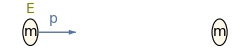

```mathematica
a1=2;r=0.4;
p1={0.0,0};
p2={10,0};
centerPlot@Graphics[{{EdgeForm[Black],FaceForm[backgroundColor1],Disk[p1,r],Disk[p2,r]},{color1,Arrow[{p1+{r,0},p1+{r,0}+a1{1,0}}],Text[font@"p",{r+a1*0.4,0.4}]},Text[font@"m",p1],Text[font@"m",p2],{color2,Text[font@"E",{0,r+0.3}]}},ImageSize->250]
```

They collide (elastically, meaning that the final masses are the same as the initial masses) in such a way that they both scatter at an angle θ relative to the incident direction. What is θ in terms of E and m? What is θ in the relativistic and non-relativistic limits?

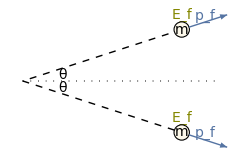

```mathematica
a2=1.2;r=0.23;θ=π/10;
p1={5 Cos[θ],5 Sin[θ]};
p2={1,-1}p1;
centerPlot@Graphics[{{Dashed,Line[{{p1,{0,0},p2}}]},{Dotted,Line[{{{0,0},{p2[[1]]+a2 Cos[θ],0}}}]},{EdgeForm[Black],FaceForm[backgroundColor1],Disk[p1,r],Disk[p2,r]},{color1,Arrow[{p1+{r Cos[θ],r Sin[θ]},p1+{r Cos[θ],r Sin[θ]}+a2{Cos[θ],Sin[θ]}}],Arrow[{p2+{r Cos[θ],-r Sin[θ]},p2+{r Cos[θ],-r Sin[θ]}+a2{Cos[θ],-Sin[θ]}}],Text[font@"p_f",p2+{r Cos[θ],-r Sin[θ]}+a2/2{Cos[θ],-Sin[θ]}+{-0.1,0.23}],Text[font@"p_f",p1+{r Cos[θ],r Sin[θ]}+a2/2{Cos[θ],Sin[θ]}+{-0.1,0.15}]},Text[font@"m",p1],Text[font@"m",p2],{color2,Text[font@"E_f",p1+{0,r+0.2}],Text[font@"E_f",p2+{0,r+0.2}]},Text[font@"θ",{1.2,0.17}],Text[font@"θ",{1.2,-0.20}]},ImageSize->250]
```

Solution 
As in all collision problems, we begin by writing down the energy and momentum conservation laws for this system:

Conservation of Energy: E+m c^2=2E'

Conservation of Momentum (in the x-direction): p=2p'Cos[θ]

Invariant mass of the moving particle in the initial setup: E^2-p^2 c^2=m^2 c^4

Invariant mass of either moving particle in the final setup: E'^2-p'^2 c^2=m^2 c^4

The rest is just careful algebra! Here we solve these four equations for the four unknowns (E',p',p,and θ) using Mathematica

```mathematica
sol=FullSimplify[Last@Solve[{p==2pf cosθ,Ε+m c^2==2Εf,Εf^2-pf^2 c^2==m^2 c^4,Ε^2-p^2 c^2==m^2 c^4},{Εf,p,pf,cosθ}],0<Ε&&0<m&&0<c]
```

{Εf→1/2 (c^2 m+Ε),p→(√(-c^4 m^2+Ε^2))/c,pf→(√(-3 c^4 m^2+2 c^2 m Ε+Ε^2))/(2 c),cosθ→√((c^2 m+Ε)/(3 c^2 m+Ε))}

Alternatively, the algebra simplifies quite a bit if you use the 4-momenta

P_1=(E/c,p,0,0)

P_2=(m c,0,0,0)

where p c=√(E^2-m^2 c^4). The 4-momenta after the collision are (primes now denote “after”)

P_1'=(E'/c,p'Cos[θ],p'Sin[θ],0)

P_2'=(E'/c,p'Cos[θ],-p'Sin[θ],0)

where p' c=√(E'^2-m^2 c^4). Conservation of energy gives E'/c=1/2(E/c+m c), and conservation of p_x gives p'Cos[θ]=p/2. Therefore, the 4-momenta after the collision are

P_(1/2)'=(E/(2c)+(m c)/2,p/2,±p/2Tan[θ],0)

As discussed above, P^2≡P·P=m^2 c^2. Therefore,

m^2 c^2=(E/(2c)+(m c)/2)^2-(p/2)^2(1+Tan[θ]^2)

4 m^2 c^4=(E+m c^2)^2-(E^2-m^2 c^4)/Cos[θ]^2

(E^2-m^2 c^4)/Cos[θ]^2=E^2+2E m c^2-3 m^2 c^4

Cos[θ]^2=(E^2-m^2 c^4)/(E^2+2E m c^2-3 m^2 c^4)=(E+m c^2)/(E+3m c^2)

Now let us consider the relativistic and non-relativistic limits:

```mathematica
Echo[Series[cosθ/.sol,{Ε,∞,1}],"Relativistic Limit of Cos[θ]:"];
Echo[FullSimplify[cosθ/.sol/.Ε->m c^2],"Non-Relativistic Limit of Cos[θ]:"];
```

Relativistic Limit of Cos[θ]: 1-(c^2 m)/Ε+O[1/Ε]^2

Non-Relativistic Limit of Cos[θ]: 1/(√2)

The relativistic limit is E≫m c^2, which yields Cos[θ]≈1. Therefore, both particles scatter almost directly forward.

The non-relativistic limit is E≈m c^2 (it is not E≈0), which yields Cos[θ]≈1/(√2). Therefore, θ≈45°, and the particles scatter with a 90° angle between them. This agrees with the result from Classical Mechanics which states that when a particle of mass m collides with another particle of mass m at rest, the two particles will scatter with a 90° angle between them. □

Note that the above problem is only one possible scenario when a mass m slams into another mass m at rest. The two particles could also have moved at different final angles, which would implied that they have different momenta (to conserve momentum in the y-direction) and therefore different energies (since E^2=p^2 c^2+m^2 c^4). You could work through this more general case, and the answer must reduce to that found above when the two angles are equal.

#### Complementary Section: Decay at an Angle

Example 
A particle with mass M and energy E decays into two identical particles. In the lab frame, they are emitted at angles 90° and θ. What are the energies of the created particles?

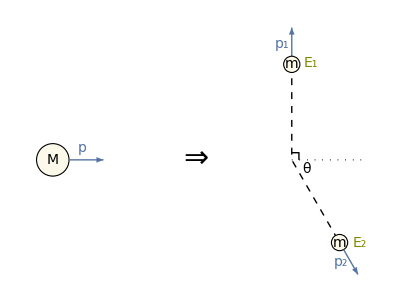

```mathematica
a2=1.2;r=0.17;θ=-π/3;
p0={-5,0};
p1={0,2};
p2=2{Cos[θ],Sin[θ]};
centerPlot@Graphics[{{Dashed,Line[{{p1,{0,0},p2}}]},{Line[1.5{{0.1,0},{0.1,0.1},{0,0.1}}],Dotted,Line[{{{0,0},{3Cos[θ],0}}}]},{EdgeForm[Black],FaceForm[backgroundColor1],Disk[p0,2r],Disk[p1,r],Disk[p2,r]},{color1,Arrowheads[0.025],Arrow[{p0+{2r,0},p0+{2r,0}+{0.6a2,0}}],Arrow[{p1+{0,r},p1+{0,r+a2/2}}],Arrow[{p2+{r Cos[θ],r Sin[θ]},p2+{r Cos[θ],r Sin[θ]}+a2/2{Cos[θ],Sin[θ]}}],Text[font@"p",p0+{r,0}+{0.45,0.25}],Text[font@"p_2",p2+{r Cos[θ],r Sin[θ]}+a2/2{Cos[θ],Sin[θ]}+{-0.35,0.25}],Text[font@"p_1",p1+{0,r+a2/2}+{-0.2,-0.35}]},Text[font["⇒",30],{-2,0}],Text[font@"M",p0],Text[font@"m",p1],Text[font@"m",p2],{color2,Text[font@"E_1",p1+{0.4,r-0.15}],Text[font@"E_2",p2+{r+0.25,0}]},Text[font@"θ",{0.3,-0.20}]}]
```

Solution
Method 1: The energy E and momentum p before the decay must satisfy p c=√(E^2-M^2 c^4). Denote the masses of the created particles be m as shown in the figure above. After the collision, the total energy equals E_1+E_2 and the total momentum equals (p_2 Cos[θ],p_1-p_2 Sin[θ],0).

Conservation of momentum in the x-direction immediately gives p_2 Cos[θ]=p, and conservation in the y-direction then implies p_1=p_2 Sin[θ]=p Tan[θ]. In other words, the total momenta of the two particles after the collision are

(p⃗)_1=(0,p Tan[θ],0)

(p⃗)_2=(p,-p Tan[θ],0)

Conservation of energy gives E=E_1+E_2. Writing this in terms of the momenta and masses gives

E=√(p^2 c^2 Tan[θ]^2+m^2 c^4)+√(p^2 c^2(1+Tan[θ]^2)+m^2 c^4)

Bringing the first radical to the left side, squaring, and simplifying yields

(E-√(p^2 c^2 Tan[θ]^2+m^2 c^4))^2=p^2 c^2(1+Tan[θ]^2)+m^2 c^4

E^2+p^2 c^2 Tan[θ]^2+m^2 c^4-2E √(p^2 c^2 Tan[θ]^2+m^2 c^4)=p^2 c^2(1+Tan[θ]^2)+m^2 c^4

√(p^2 c^2 Tan[θ]^2+m^2 c^4)=(E^2-p^2 c^2)/(2E)

Noting that the left hand side equals E_1, we find

E_1=(E^2-p^2 c^2)/(2E)=(M^2 c^4)/(2E)

In a similar manner, we find that E_2 equals

E_2=(E^2+p^2 c^2)/(2E)=(2 E^2-M^2 c^4)/(2E)

These add up to E, as they should.

Method 2: We can solve this problem using the 4-momenta

P=(E/c,p,0,0)

P_1=(E_1/c,0,p_1,0)

P_2=(E_2/c,p_2 Cos[θ],-p_2Sin[θ],0)

Conservation of energy and momentum can be combined into the statement, P=P_1+P_2. Therefore,

P-P_1=P_2

(P-P_1)·(P-P_1)=P_2·P_2

P^2-2P_1·P+P_1^2=P_2^2

M^2 c^2-2 E_1/c E/c+m^2 c^2=m^2 c^2

E_1=(M^2 c^4)/(2E)

And then E_2=E-E_1=((2 E^2-M^2 c^4)/(2E)).

This solution should convince you that 4-momenta can save you a lot of work. What happened here was that the expression for P_2 was fairly messy, but we arranged things so that it only appeared in the form of P_2^2, which is simply m^2 c^2. 4-momenta provide a remarkably organized method for sweeping unwanted garbage under the rug. □

#### Complementary Section: Increase in Mass

Example 
A large mass M, moving with speed v, collides and sticks to a small mass m, initially at rest. What is the mass M_f of the resulting object? Work in the approximation where M≫m.

Solution 
In the lab frame, the final energy (divided by c), E_f/c, of the resulting object is γ M c+m c, and the momentum is still γ M v where γ=1/((1-v^2/c^2)^(1/2)). The mass of the object is therefore

M_f c=√((γ M c+m c)^2-(γ M v)^2)=√(M^2 c^2+2γ M m c^2+m^2 c^2)

The m^2 term is negligible compared to the other two terms, so we may approximate M_f as

M_f c≈√(M^2 c^2+2γ M m c^2)=M c √(1+2γ m/M)≈M c (1+γ m/M)

where we have used the Taylor series √(1+ϵ)≈1+ϵ/2. Therefore, the increase in mass is γ times the mass of the stationary object.

M_f=M+γ m

Note that this increase in mass must be greater than the non-relativistic answer of m, because heat is generated during the collision, and in General Relativity this heat shows up as mass in the final object. Also, the γ m result is much clearer if we work in the frame where M is initially at rest. In this frame, the mass m comes flying in with energy γ m c^2, and essentially all of this energy shows up as mass in the final object. That is, essentially none of it shows up as overall kinetic energy of the object.

To be more quantitative, we could solve for the final mass M_f and the final speed v_f of the object in the limit M≫m using conservation of energy and momentum. The Mathematica code below shows that (to first order),

M_f=M+γ m

v_f=v-v/γ m/M

```mathematica
$Assumptions=0<v<c&&0<m&&0<M;
Simplify[Series[{Mf,vf}/.Simplify[Solve[{γ M c+m c==γf Mf c,γ M v==γf Mf vf}/.{γf->1/((1-vf^2/c^2)^(1/2)),γ->1/((1-v^2/c^2)^(1/2))},{Mf,vf}]],{m,0,1}]]
```

{{M+(c m)/(√(c^2-v^2))+O[m]^2,v-(v √(c^2-v^2) m)/(c M)+O[m]^2}}

Therefore, in the frame where the mass M is initially at rest, the final velocity of the mass M_f would be of the order O[m/M]. This is a general result. Stationary large objects pick up negligible kinetic energy when hit by small objects. This is true because the speed of the large object is proportional to m/M by momentum conservation (there's a factor of γ if things are relativistic), so the kinetic energy goes like M v^2∝M (m/M)^2≈0, if M≫m. In other words, the smallness of v wins out over the largeness of M. When a snowball hits a tree, all of the initial energy goes into heat to melt the snowball; (essentially) none of it goes into changing the kinetic energy of the earth. □

#### Two-Body Decay

Example
A mass M_A decays into masses M_B and M_C. What are the energies of M_B and M_C? What are their momenta?

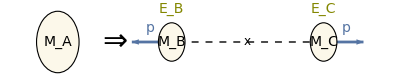

```mathematica
a2=1.4;r=0.35;θ=-π/3;
p0={-5,0};
p1={2,0};
p2={-2,0};
centerPlot@Graphics[{{Dashed,Line[{{p1,{0,0},p2}}]},{EdgeForm[Black],FaceForm[backgroundColor1],Disk[p0,1.6r],Disk[p1,r],Disk[p2,r]},{color1,Arrowheads[0.03],Thickness[0.005],Arrow[{p1+{r,0},p1+{r+a2/2,0}}],Arrow[{p2+{-r,0},p2-{r+a2/2,0}}],Text[font@"p",p2+{-0.41a2,0.25}],Text[font@"p",p1+{0.42a2,0.25}]},Text[font["⇒",30],{-3.5,0}],Text[font@"M_A",p0],Text[font@"M_C",p1],Text[font@"M_B",p2],{color2,Text[font@"E_C",p1+{0,0.6}],Text[font@"E_B",p2+{0,0.6}]},{Text[Style["x",12],{0,0}]}}]
```

Solution
Conservation of momentum shows that B and C have equal and opposite momentum, p. Thus

E_B^2/c^2-M_B^2 c^2=p^2=E_C^2/c^2-M_C^2 c^2

Conservation of energy yields

M_A c=E_B/c+E_C/c

Solving these two equations for E_B and E_C yields

E_B=(c^2 (M_A^2+M_B^2-M_C^2))/(2 M_A)

E_C=(c^2 (M_A^2-M_B^2+M_C^2))/(2 M_A)

```mathematica
Solve[{EB^2/c^2-MB^2 c^2==EC^2/c^2-MC^2 c^2,MA c==EB/c+EC/c},{EB,EC}]
```

{{EB→(c^2 (MA^2+MB^2-MC^2))/(2 MA),EC→(c^2 (MA^2-MB^2+MC^2))/(2 MA)}}

Equation (TextNumbered) then yields the momentum of the particles as

p=(c √((M_A-M_B-M_C) (M_A+M_B-M_C) (M_A-M_B+M_C) (M_A+M_B+M_C)))/(2 M_A)

```mathematica
FullSimplify@Sqrt@Together[((c (MA^2+MB^2-MC^2))/(2 MA))^2-MB^2 c^2]
```

(c √((MA-MB-MC) (MA+MB-MC) (MA-MB+MC) (MA+MB+MC)))/(2 MA)

We could also have solved this problem by explicitly writing out the velocities of B and C and then solving for their momentum, as shown using Mathematica below

```mathematica
$Assumptions=0<MC<MB<MA&&0<c;
res=First@FullSimplify@Solve[{MA c==γB MB c+γC MC c,γB MB vB==γC MC vC}/.{γB->1/((1-vB^2/c^2)^(1/2)),γC->1/((1-vC^2/c^2)^(1/2))},{vB,vC}];
(* Momentum of Subscript[M, B] *)
FullSimplify[γB MB vB/.γB->1/((1-vB^2/c^2)^(1/2))/.res]
```

(c √((MA-MB-MC) (MA+MB-MC) (MA-MB+MC) (MA+MB+MC)))/(2 MA)

Note that if M_A=M_B+M_C, then p=0 since there is no energy left over for the particles to be able to move. □

### One Final Special Relativity Concept - Doppler Effect

One final (but still very important) concept in Special Relativity is the Doppler effect, which relates the frequency of a moving object to the perceived frequency of an observer in a different reference frame.

This concept is very important, and will certainly appear on a quiz or the final. Please read Helliwell’s Section 13.2 to understand this concept. However, we shall skip it and dive straight into General Relativity!

### General Relativity

Just like the fluids in the Ph 1a, we will take a short journey into General Relativity. We won’t get to the true heart of the material - in fact, we won’t perform any calculations - but we will take a quick look at the scenery, discussing the main postulates and some of their effects. A true course in General Relativity would require a solid background in Special Relativity as well as mathematics (namely linear algebra).

#### The Postulates

Einstein’s Equivalence Principle says that it is impossible to locally distinguish between gravity and acceleration. This may be stated more precisely in (at least) three ways.

Let person A be enclosed in a small box, far from any massive objects, that undergoes uniform acceleration (say, g). Let person B stand at rest on the earth as shown in the figure below. The Equivalence Principle says that there are no local experiments these two people can perform that will tell them which of the two settings they are in. The physics of each setting is the same.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Let person A be enclosed in a small box that is in free-fall near a planet. Let person B float freely in space, far away from any massive objects as shown in the figure below. The Equivalence Principle says that there are no local experiments these two people can perform that will tell them which of the two settings they are in. The physics of each setting is the same.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

“Gravitational” mass is equal to (or proportional to) “inertial” mass. Gravitational mass is the m_g that appears in the formula, F=(G M m_g)/r^2≡m_g g. Inertial mass is the m_i that appears in the formula, F=m_i a. There is no a priori reason why these two m’s should be the same (or proportional). An object that is dropped on the earth will have acceleration a=m_g/m_i g. For all we know, the ratio m_g/m_i for plutonium is different from that for copper. But experiments with various materials have detected no difference in the ratios. The Equivalence Principle states that the ratios are equal for any type of mass.

#### Some Stories

There are many consequences of general relativity. To quantify them would require using 4-vectors and – while it would not be too difficult – we will leave these hard details for another class. For now, I will just whet your appetite with some tasty tidbits.

Time dilation: Clocks run slower close to a massive object. For example, on Earth a clock running at the top of a mountain runs faster than a clock at sea level. One measure this experimentally by firing a light beam from the top of a tower of height h to a receiver at the bottom of the tower. One could analyze this theoretically using the Equivalence Principle, which states that this situation is the same as firing light from the front of a rocket to the rear of a rocket undergoing uniform acceleration g.

```mathematica
centerPlot@Grid[{{-Graphics-,-Graphics-}},Alignment->Bottom,Spacings->{5, 1}]
```

-Graphics- | -Graphics-

As quaintly stated by David Morin:

Greetings! Dear brother from Boulder,
I hear that you’ve gotten much older.
And please tell me why
My lower left thigh
Hasn’t aged quite as much as my shoulder!

Constant acceleration: Unlike in Newtonian mechanics, constant acceleration is a tricky and unintuitive beast in General Relativity. First, consider the (seemingly obvious) fact the location in space that you are standing on now accelerates backwards away from you, getting further and further away. Now consider the (not-so-intuitive) fact that as you accelerate, the stars behind you get jump closer to you due to length contraction. So somewhere behind you there is a point that remains the same distance from you as you accelerate. If you undergo constant acceleration, this point remains the same distance from you for all time!

Black holes: The main dish of a General Relativity course is the study of black holes. As most people know, black holes have an event horizon; inside of this horizon nothing (including light) can escape. Notions of time and space become horribly muddled around black holes. For example, suppose a person decides to jump into a black hole. That person will see himself cross the event horizon in a finite amount of (proper) time, but all of his friends will see him take an infinite to fall into the event horizon. Black holes also give people great excuses to make apocalyptic movies.

## Mathematica Initialization

```mathematica
(* Primary colors for figures *)
colors={color1,color2,color3,color4,color5,color6}={Darker[ColorData[97][1],0.1],Darker[ColorData[97][10],0.1],ColorData[97][5],ColorData[97][6],ColorData[97][9],Lighter@ColorData[97][7]}
(* Secondar colors for backgrounds *)
backgroundColors={backgroundColor1}={RGBColor[0.99, 0.97432, 0.91748]};
```

{RGBColor[0.3315753, 0.4561011, 0.6388182],RGBColor[0.5144301, 0.5278347, 0.],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.575932, 0.7456673333333332, 0.8548993333333333]}

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```